```mathematica
SetDirectory[NotebookDirectory[]]
```

/Users/oernst/github_public_repos/d-Cubic/examples

Grid

```mathematica
grid=Import["test_deriv_p_1d.txt","Table"];
```

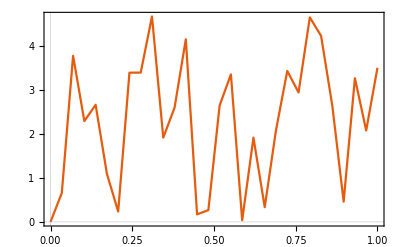

```mathematica
ListLinePlot[grid]
```

```mathematica
xSpacing=Abs[grid[[2,1]]-grid[[1,1]]]
```

0.034483

Analytic formula

```mathematica
derivp0=-0.5 x+x^2-0.5 x^3
```

-0.5 x+x^2-0.5 x^3

```mathematica
derivp1=1-2.5 x^2+1.5 x^3
```

1-2.5 x^2+1.5 x^3

```mathematica
derivp2=0.5 x+2. x^2-1.5 x^3
```

0.5 x+2. x^2-1.5 x^3

```mathematica
derivp3=-0.5 x^2+0.5 x^3
```

-0.5 x^2+0.5 x^3

Test point

```mathematica
xTest=0.71;
```

Convert to fraction

```mathematica
pt1=Select[grid,#[[1]]>xTest-xSpacing&&#[[1]]<xTest&][[1]]
```

{0.689655,2.08743}

```mathematica
xFrac=(xTest-pt1[[1]])/xSpacing
```

0.590001

Evaluate test

```mathematica
derivp0/.x->xFrac
```

-0.0495894

```mathematica
derivp1/.x->xFrac
```

0.437817

```mathematica
derivp2/.x->xFrac
```

0.683133

```mathematica
derivp3/.x->xFrac
```

-0.0713606